```mathematica
MVVerlet[x0_, v0_, m_, q_, dt_, n_, BF_] := 
Module[{X, V, alpha, x,v,d,C,j},
X = Table[0.,{i,1,n}];
X[[1]]=x0;
V = Table[0.,{i,1,n}];
V[[1]]=v0;
x = x0;
v = v0;
alpha = q dt /(2m);
For[j = 2, j <= n, j = j+1,
d = v+ alpha Cross[v, BF[x]];
x = x +d dt;
C = BF[x];
v = (d + alpha Cross[d,C] + alpha^2 C d.C)/(1+alpha^2 C.C);
X[[j]]=x;
V[[j]]=v;
];
Return[{X,V}];
]
```

```mathematica
ShowTrajectory[pts_] := Show[Graphics3D[Table[Line[{pts[[jj]],pts[[jj+1]]}],{jj,1,Length[pts]-1}]]]
```

```mathematica
dt = 0.005
n = 5000
x0 = {1,0,0}
v0 = {0,1,0.1}
BF[{x_,y_,z_}]={0,0,1}
m=1
q=1
```

0.005

50000

{1,0,0}

{0,1,0.1}

{0,0,1}

1

1

```mathematica
{X,V} =MVVerlet[x0,v0,m,q,dt,n,BF]
```

```mathematica
ShowTrajectory[X]
```

-Graphics3D-

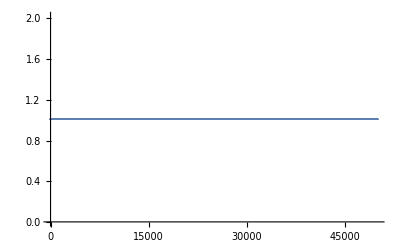

```mathematica
vsquared = Table[V[[jj]].V[[jj]],{jj,1,Length[V]}];
ListPlot[vsquared]
```

{1,0,0}

{0.,0.1,0.3}

{y,-x,0}

-Graphics3D-

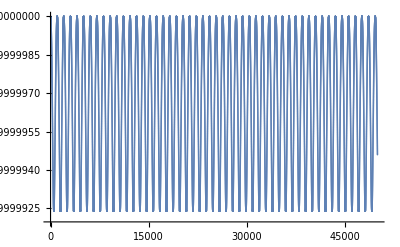

```mathematica
x0 = {1,0,0}
v0 = {0.0,0.1,0.3}
n = 50000
BF[{x_,y_,z_}]={y,-x,0}
{X,V} =MVVerlet[x0,v0,m,q,dt,n,BF]
ShowTrajectory[X]
vsquared = Table[V[[jj]].V[[jj]],{jj,1,Length[V]}];
ListPlot[vsquared]
```

{1,0,0}

{0.,0.05,0.05}

50000

{y,-x,0}

-Graphics3D-

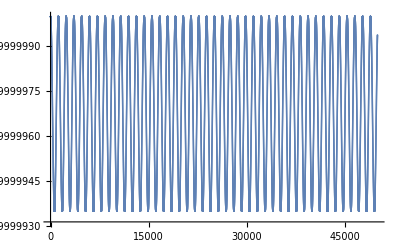

```mathematica
x0 = {1,0,0}
v0 = {0.0,0.05,0.05}
n = 50000
BF[{x_,y_,z_}]={y,-x,0}
{X,V} =MVVerlet[x0,v0,m,q,dt,n,BF]
ShowTrajectory[X]
vsquared = Table[V[[jj]].V[[jj]],{jj,1,Length[V]}];
ListPlot[vsquared]
```